# Angular Correlation

Authors: Giovanni Bocchi
Contact: giovanni.bocchi@gmail.com
Version: 1.1.1
Last update: 13 June 2019

Description of the program: ... to do!!

1. Create a csv file with the following structure: 4 columns separated by comma
- angle: angle expressed in degree
- counts: integral
- errors: integral error
- normalization: number of couples for that particular angle 

<angle>,	 <counts>, 	<errors>, 	<normalization>
...,			...,				...,				...
...,			...,				...,				...
...,			...,				...,				...

2. Put the input and the notebook file in the same folder
3. Fill the yellow cell
4. Evaluate the entire notebook

```mathematica
(* CLEAR VARIABLES *)
Clear[A2,A1,W,f,AA2,AA4,δ1,δ2,delta1,delta2,solut1,estremanti,posimo,numestr,chi2,chiestr,chiquadro1,chiquadro2,ii,ff,mm1,mm2, A00, A22, A44, cl, L1max, L2max, input,data];

(* CONFIDENCE LEVEL *)
cl=0.95;

(* WRITE THE 2 ENERGIES IN keV *)
g1=5853;
g2=649;

(* CHOOSE ONE OF THE NEXT 3 OPTIONS
param = 0 ------> δ1 = fixed, δ2 = fixed;
param = 1 ------> δ1 = free, δ2 = fixed; 
param = 2 ------> δ1 = fixed, δ2 = free;
*)
param=0;
delta1=0.0;
delta2=0.0;

(* WRITE THE SPIN OF THE 4 STATES *)
ii=0;
mm1=1;
mm2=1;
ff=0;

(* WRITE THE MULTIPOLARITY OF THE γ-RAYS. IF THERE IS NO MIXING INSERT THE SAME VALUE TWO TIMES *)
L1=1;
lL1=1;
L2=1;
lL2=1;

(* WRITE THE ATTENUATION COEfinalStateICIENTS *)
q1=0.94;
q2=0.85;
```

RESULTS:

Summary:

---------------------- 0

| 5853 keV

|

| γ1

|

|

V

---------------------- 1

| 649 keV

|

| γ2

|

|

V

---------------------- 0

Energy First γ-ray = 5853 keV

Energy Second γ-ray = 649 keV

Spin Initial State = 0

Spin Intermediate State = 1

Spin Final State = 0

Mix First Transition = δ1

Mix Second Transition = δ2

Multipolarity of the First Transition = 1

Multipolarity of the Second Transition = 1

Experimental Angular Correlation:  W(ϑ)= A_00(1 + Q_1A_22P_2(cosϑ))

| Estimate | Standard Error | t-Statistic | P-Value
A00 | 20606.1 | 58.3389 | 353.214 | 2.64256×10^-34
A22 | 0.479871 | 0.00684105 | 70.1459 | 2.21336×10^-22

| Estimate | Standard Error | Confidence Interval
A00 | 20606.1 | 58.3389 | {20483.1,20729.2}
A22 | 0.479871 | 0.00684105 | {0.465438,0.494304}

| DF | SS | MS
Model | 2 | 513778. | 256889.
Error | 17 | 67.6931 | 3.98195
Uncorrected Total | 19 | 513846. | 
Corrected Total | 18 | 20324.8 |

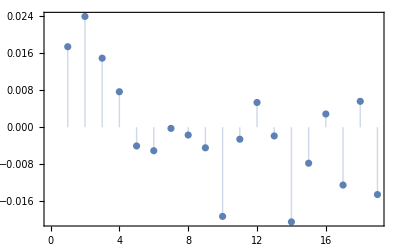

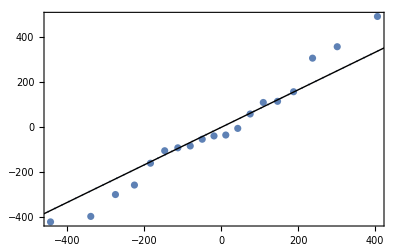

R^2(adj): 0.999853

R^2: 0.999868

Theoretical Angular Correlation:   W(ϑ): 1 + Q_1A_22P_2(cosϑ)

A22 (Theory) = 0.5

δ1 = 0.

δ2 = 0.

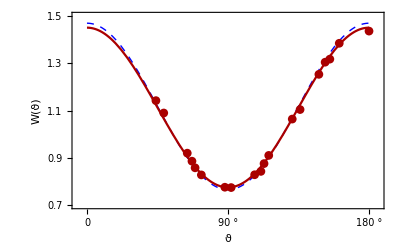

```mathematica
(* PROGRAM *)
Needs["ErrorBarPlots`"];

(* IMPORT EXPERIMENTAL DATA *)
input=Import[StringJoin[NotebookDirectory[],"input.csv"]];

(* UPPER LIMIT OF THE SUM *)
L1max=Max[L1, lL1];
L2max=Max[L2, lL2];
min=If[EvenQ[Min[2*mm1,2*mm2,2*L1max,2*L2max]]==True,
Min[2*mm1,2*mm2,2*L1max,2*L2max],
Min[2*mm1,2*mm2,2*L1max,2*L2max]-1
];

(* DATA PREPARATION *)
inputAngles=input[[All,1]];
inputCounts=input[[All,2]];
inputErrors=input[[All,3]];
inputNorm=input[[All,4]];
inputAngles=inputAngles Degree;
wNorm=inputCounts/inputNorm;
error=inputErrors/inputNorm;
data=Transpose[{inputAngles,wNorm}];

(* EXPERIMENTAL FIT *)
(* DEFINE THE MOST GENERAL FUNCTION *)
W[θ_,aa00_,aa22_,aa44_,q1_,q2_]:=aa00*(1+aa22 *q1*LegendreP[2,Cos[θ]]+aa44 *q2*LegendreP[4,Cos[θ]]);

(* NON LINEAR FIT *)
If[min==2,
nlf=
NonlinearModelFit[
data,
W[θ,A00,A22 ,0,q1,q2],
{A00,A22},
θ,
Weights->1/error^2 (*, ßVarianceEstimatorFunction->(1&)*),
ConfidenceLevel->cl
]
];
If[min==4,
nlf=
NonlinearModelFit[
data,
W[θ,A00,A22 ,A44,q1,q2],
{A00,A22,A44},
θ,
Weights->1/error^2 (*, ßVarianceEstimatorFunction->(1&)*),ConfidenceLevel->cl
]
];

(* NORMALIZED DATA *)
norm = nlf[[1,2,1,2]];
wNormA0=wNorm/norm;
datanormA0=Transpose[{inputAngles,wNormA0}];
errornormA0=inputErrors/inputNorm/norm;

(* CONFIDENCE INTERVAL 80%, 90%, 95% AND 99%*)
{bands80[θ_],bands90[θ_],bands95[θ_],bands99[θ_]}=Table[nlf["SinglePredictionBands",ConfidenceLevel->cl],{cl,{.9,.95,.99,.999}}];

(* SCHEMATIC PLOT OF THE CASCADE*)
If[
mm1==mm2,
Print[Text[Style["RESULTS:",FontSize->30,Bold,Red]]];
Print[Text[Style["Summary:",Large,Blue]]];
Print["---------------------- ",ii];
Print["       | ",g1," keV"];
Print["       | "];
Print["       | γ1"];
Print["       | "];
Print["       | "];
Print["       V "];
Print["---------------------- ",mm1];
Print["          | ",g2," keV"];
Print["          | "];
Print["          | γ2"];
Print["          | "];
Print["          | "];
Print["          V "];
Print["---------------------- ",ff];
Print["Energy First γ-ray = ",g1," keV"];
Print["Energy Second γ-ray = ",g2," keV"];
Print["Spin Initial State = ",ii];
Print["Spin Intermediate State = ",mm1];
Print["Spin Final State = ",ff];
Print["Mix First Transition = ",δ1];
Print["Mix Second Transition = ",δ2];
If[L1==lL1,
Print["Multipolarity of the First Transition = ",L1]
];
If[L1!=lL1,
Print["Multipolarity of the First Transition = ",L1," and ",lL1]
];
If[L2==lL2,
Print["Multipolarity of the Second Transition = ",L2]
];
If[L2!=lL2,
Print["Multipolarities of the Second Transition = ",L2," and ",lL2]
]
]
If[
mm1!=mm2,
Print[Text[Style["RESULTS:",FontSize->30,Bold,Red]]];
Print[Text[Style["Summary:",Large,Blue]]];
Print["---------------------- ",ii];
Print["       | ",g1," keV"];
Print["       | "];
Print["       | γ1"];
Print["       | "];
Print["       | "];
Print["       V "];
Print["---------------------- ",mm1];
Print[""];
Print[""];
Print["---------------------- ",mm2];
Print["          | ",g2," keV"];
Print["          | "];
Print["          | γ2"];
Print["          | "];Print["          | "];
Print["          V "];
Print["---------------------- ",ff];
Print["Energy First γ-ray = ",g1," keV"];
Print["Energy Second γ-ray = ",g2," keV"];
Print["Spin Initial State = ",ii];
Print["Spin Intermediate State = ",mm1];
Print["Spin Final State = ",ff];
Print["Mix First Transition = ",δ1];
Print["Mix Second Transition = ",δ2];
If[L1==lL1,
Print["Multipolarity of the First Transition = ",L1]
];
If[L1!=lL1,
Print["Multipolarity of the First Transition = ",L1," and ",lL1]
];
If[L2==lL2,
Print["Multipolarity of the Second Transition = ",L2]
];
If[L2!=lL2,
Print["Multipolarities of the Second Transition = ",L2," and ",lL2]
]
]
Print[""];

(* PRINT TITLE EXPERIMENTAL ANALYSIS*)
If[min==2,
Print[Text[Style["Experimental Angular Correlation:  W(ϑ)= \!\(\*SubscriptBox[\(A\), \(00\)]\)(1 + \!\(\*SubscriptBox[\(Q\), \(1\)]\)\!\(\*SubscriptBox[\(A\), \(22\)]\)\!\(\*SubscriptBox[\(P\), \(2\)]\)(cosϑ))",Large,Blue]]]]
If[min==4,
Print[Text[Style["Experimental Angular Correlation:  W(ϑ)= \!\(\*SubscriptBox[\(A\), \(00\)]\)(1 + \!\(\*SubscriptBox[\(Q\), \(1\)]\)\!\(\*SubscriptBox[\(A\), \(22\)]\)\!\(\*SubscriptBox[\(P\), \(2\)]\)(cosϑ) +  \!\(\*SubscriptBox[\(Q\), \(2\)]\)\!\(\*SubscriptBox[\(A\), \(44\)]\)\!\(\*SubscriptBox[\(P\), \(4\)]\)(cosϑ))",Large,Blue]]]]

(* PRINT NLM RESULTS *)
Print[""]
nlf["ParameterTable"]
Print[""]
nlf["ParameterConfidenceIntervalTable"]
Print[""]
nlf["ANOVATable"]
Print[""]
ListPlot[nlf["FitResiduals"]/norm,Filling->Axis, Frame->True]
Print[""]
QuantilePlot[nlf["FitResiduals"]]
Print[""]
Print[ToExpression[SuperscriptBox["R","2"]],"(adj): ",nlf["AdjustedRSquared"]]
Print[""]
Print[ToExpression[SuperscriptBox["R","2"]],": ",nlf["RSquared"]]
Print[""]
(*
Print["A00 (Fit) = ",norm, " +/- ",nlf["ParameterTable"]⟦1,1,2,3⟧ ]
Print["A22 (Fit) = ",nlf[[1,2,2,2]], " +/- ",nlf["ParameterTable"]⟦1,1,3,3⟧ ]
If[min==4,Print["A44 (Fit) = ",nlf[[1,2,3,2]], " +/- ",nlf["ParameterTable"]⟦1,1,4,3⟧ ]]
*)

(*  ------------------------------------------------------------- THEORETICAL CALCULATIONS -----------------------------------------------------------------------  *)

(* PRINT TITLE *)
If[min==2,
Print[Text[Style["Theoretical Angular Correlation:   W(ϑ): 1 + \!\(\*SubscriptBox[\(Q\), \(1\)]\)\!\(\*SubscriptBox[\(A\), \(22\)]\)\!\(\*SubscriptBox[\(P\), \(2\)]\)(cosϑ)",Large,Blue]]]];
If[min==4,Print[Text[Style["Theoretical Angular Correlation:   W(ϑ): 1 + \!\(\*SubscriptBox[\(Q\), \(1\)]\)\!\(\*SubscriptBox[\(A\), \(22\)]\)\!\(\*SubscriptBox[\(P\), \(2\)]\)(cosϑ) +  \!\(\*SubscriptBox[\(Q\), \(2\)]\)\!\(\*SubscriptBox[\(A\), \(44\)]\)\!\(\*SubscriptBox[\(P\), \(4\)]\)(cosϑ)",Large,Blue]]]];

Which[
(* PARAM = 1: δ1 FREE AND δ2 FIXED *)
param==1,

(* THEORETICAL CALCULATION *)
f[L_,LL_,i_,f_]:=(-1)^(-1+i+f) ThreeJSymbol[{L,1},{LL,-1},{k,0}] √((2 f+1) (2 k+1) (2 L+1) (2 LL+1)) SixJSymbol[{L,LL,k},{f,f,i}];
A1[k_,δ1_]=1/(δ1^2+1)((-1)^(L1+lL1)2 δ1 f[L1,lL1,ii,mm1]+f[L1,L1,ii,mm1]+δ1^2 f[lL1,lL1,ii,mm1]);
A2[k_]=(2 delta2 f[L2,lL2,ff,mm2]+f[L2,L2,ff,mm2]+delta2^2 f[lL2,lL2,ff,mm2])/(delta2^2+1);

AA2=A1[2,δ1]*A2[2];
If[min==4,AA4=A1[4,δ1]*A2[4]];

If[min==2,
chi2=((nlf[[1,2,2,2]]-AA2)/(nlf["ParameterTable"]⟦1,1,3,3⟧))^2];
If[min==4,
chi2=((nlf[[1,2,2,2]]-AA2)/(nlf["ParameterTable"]⟦1,1,3,3⟧))^2+((nlf[[1,2,3,2]]-AA4)/(nlf["ParameterTable"]⟦1,1,4,3⟧))^2];

estremanti=Solve[D[chi2,δ1]==0,δ1];

(* gli estremanti saranno pari, 2 MAX e due min e alternati. controllo se i primi due sono M,m o m,M *)
numestr=Length[estremanti];
chiestr=Table[chi2/.estremanti[[i]],{i,1,numestr}];

(* se funziona ho ordinato in modo che le posizioni dispari siano minimi*)
(* bisogna capire se sono sempre 2 min e 2 MAX. per ora lo assumo *)
If[
chiestr[[1]]>chiestr[[2]],
estremanti=Reverse[estremanti],
estremanti=estremanti
];

solut1=estremanti[[1,1,2]];
solut2=estremanti[[3,1,2]];
Print[solut1];
Print[solut2];
chiquadro1=chi2/.δ1->solut1;
chiquadro2=chi2/.δ1->solut2;

(* da sistemare *)
errorchi2=NSolve[chi2==chiquadro1+1,δ1];
AppendTo[errorchi2,{δ1->solut1}];
errorchi2=Sort[errorchi2];
dove=Position[errorchi2,{δ1->solut1}][[1,1]];
sxchi2=-errorchi2[[dove-1,1,2]]+solut1;
dxchi2=errorchi2[[dove+1,1,2]]-solut1;

errorchi22=NSolve[chi2==chiquadro2+1,δ1];
AppendTo[errorchi22,{δ1->solut2}];
errorchi22=Sort[errorchi22];
dove=Position[errorchi22,{δ1->solut2}][[1,1]];
sxchi22=-errorchi22[[dove-1,1,2]]+solut2;
dxchi22=errorchi22[[dove+1,1,2]]-solut2;

chi2=chi2/.δ1->Tan[δ1];

Print["--------- Solution 1 --------------"];
Print["A22 (Theory) = ",A1[2,solut1]*A2[2] ];
Print["A44 (Theory) = ",A1[4,solut1]*A2[4]];

Print["δ1 = ",solut1,"(",-sxchi2,",",dxchi2,")"];
Print["δ2 = ",delta2];
Print["χ2 = ",chiquadro1];
Print["--------- Solution 2 --------------"];
Print["A22 (Theory) = ",A1[2,solut2]*A2[2] ];
Print["A44 (Theory) = ",A1[4,solut2]*A2[4]];

Print["δ1 = ",solut2,"(",-sxchi22,",",dxchi22,")"];
Print["δ2 = ",delta2];
Print["χ2 = ",chiquadro2];
Print["------------------------------"];

Print[
Plot[
chi2,
{δ1,-π/2,π/2},
(*{δ1,-100,100},*)
AspectRatio->1/2,
AxesLabel->{"ArcTan(δ)",χ2},
PlotStyle->Directive[Red,Thickness[0.003]],
Epilog->{PointSize[0.02] ,Point[{{ArcTan[solut1],chiquadro1},{ArcTan[solut2],chiquadro2}}]}
]
];



punto1=ParametricPlot[
(*{
{norm,nlf[[1,2,2,2]]},
*)
{AA2,AA4},
(*
{A1[2,solut1]*A2[2],A1[4,solut1]*A2[4]}
},
*)
{δ1,-100,100},
PlotRange->All,
AspectRatio->1/3,
Frame->True,
FrameLabel->{"A_22","A_44"},
Axes->{False,False},
PlotStyle->{Red,Directive[Red,Thickness[0.005]]},
Epilog->{PointSize[0.02],Point[{{A1[2,solut1]*A2[2],A1[4,solut1]*A2[4]},{A1[2,solut2]*A2[2],A1[4,solut2]*A2[4]}},VertexColors->{Blue}]}
];
punto2=ErrorListPlot[{{{nlf[[1,2,2,2]],nlf[[1,2,3,2]]},ErrorBar[nlf["ParameterTable"]⟦1,1,3,3⟧ ,nlf["ParameterTable"]⟦1,1,4,3⟧ ]}}] ;
punto3=ErrorListPlot[{{{nlf[[1,2,2,2]],nlf[[1,2,3,2]]},ErrorBar[nlf["ParameterTable"]⟦1,1,3,3⟧ ,nlf["ParameterTable"]⟦1,1,4,3⟧ ]}}] ;

Print[Show[{punto1,punto2,punto3}]];


Experiment=
ListPlot[datanormA0,
PlotStyle->{PointSize[0.05],Darker[Red]},
PlotMarkers->Automatic,
PlotRange->{{0,π},{0.7,1.5}}
];


Theory=Plot[
W[θ,1,A1[2,solut1]*A2[2] ,A1[4,solut1]*A2[4],q1,q2],
{θ,0,π},
PlotStyle->{Blue,Dashed,Thick},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];


Theory2=Plot[
W[θ,1,A1[2,solut2]*A2[2] ,A1[4,solut2]*A2[4],q1,q2],
{θ,0,π},
PlotStyle->{Blue,Dashed,Thick},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];


fit2=
Plot[
W[θ,norm,nlf[[1,2,2,2]],nlf[[1,2,3,2]],q1,q2]/norm,
{θ,0,π},
PlotStyle->Darker[Red],
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];


errori=
ErrorListPlot[
Transpose[{datanormA0,Map[ErrorBar,errornormA0]}],
PlotStyle->Darker[Red]
];




bands=Plot[{fit2,bands99[θ]/norm},{θ,0,Pi},Filling->{2->{1}}];


results=
Show[
{
(*bands,*)
Theory,
Experiment,
(*fit2,*)
errori
},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}},
Frame->True,FrameTicks->{{{0.7,0.9,1.1,1.3,1.5},None},{{0°,90°,180°},None}},FrameTicksStyle->Directive[Black,16],
AxesLabel->{Style[ϑ,Black],Style[W[ϑ],Black]},LabelStyle->Directive[Black]
];
results2=
Show[
{
Theory2,
Experiment,
(*fit2,*)
errori
},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}},
Frame->True,FrameTicks->{{{0.7,0.9,1.1,1.3,1.5},None},{{0°,90°,180°},None}},FrameTicksStyle->Directive[Black,16],
AxesLabel->{Style[ϑ,Black],Style[W[ϑ],Black]},LabelStyle->Directive[Black]
];


Print[{results,results2}];

,




(* PARAM = 2: δ1 FIXED AND δ2 FREE *)
param==2,

(* THEORETICAL CALCULATION *)
f[L_,LL_,i_,f_]:=(-1)^(-1+i+f) ThreeJSymbol[{L,1},{LL,-1},{k,0}] √((2 f+1) (2 k+1) (2 L+1) (2 LL+1)) SixJSymbol[{L,LL,k},{f,f,i}];
A1[k_]=1/(delta1^2+1)((-1)^(L1+lL1)2 delta1 f[L1,lL1,ii,mm1]+f[L1,L1,ii,mm1]+delta1^2 f[lL1,lL1,ii,mm1]);
A2[k_,δ2_]=1/(δ2^2+1)(2 δ2 f[L2,lL2,ff,mm2]+f[L2,L2,ff,mm2]+δ2^2 f[lL2,lL2,ff,mm2]);

AA2=A1[2]*A2[2,δ2];
AA4=A1[4]*A2[4,δ2];

If[min==2,
chi2=((nlf[[1,2,2,2]]-AA2)/(nlf["ParameterTable"]⟦1,1,3,3⟧))^2];
If[min==4,
chi2=((nlf[[1,2,2,2]]-AA2)/(nlf["ParameterTable"]⟦1,1,3,3⟧))^2+((nlf[[1,2,3,2]]-AA4)/(nlf["ParameterTable"]⟦1,1,4,3⟧))^2];

estremanti=Solve[D[chi2,δ2]==0,δ2];
numestr=Length[estremanti];
chiestr=Table[chi2/.estremanti[[ i]],{i,1,numestr}];

If[
chiestr[[1]]>chiestr[[2]],
estremanti=Reverse[estremanti],
estremanti=estremanti
];

solut1=estremanti[[1,1,2]];
solut2=estremanti[[3,1,2]];

(*
posminimo=Position[chiestr,Min[chiestr]];
solut2=estremanti[[posminimo[[1,1]]]][[1,2]];
*)
chiquadro1=chi2/.δ2->solut1;
chiquadro2=chi2/.δ2->solut2;

errorchi2=NSolve[chi2==chiquadro1+1,δ2];
AppendTo[errorchi2,{δ2->solut1}];
errorchi2=Sort[errorchi2];
dove=Position[errorchi2,{δ2->solut1}][[1,1]];
sxchi2=-errorchi2[[dove-1,1,2]]+solut1;
dxchi2=errorchi2[[dove+1,1,2]]-solut1;

errorchi22=NSolve[chi2==chiquadro2+1,δ2];
AppendTo[errorchi22,{δ2->solut2}];
errorchi22=Sort[errorchi22];
dove=Position[errorchi22,{δ2->solut2}][[1,1]];
sxchi22=-errorchi22[[dove-1,1,2]]+solut2;
dxchi22=errorchi22[[dove+1,1,2]]-solut2;

chi2=chi2/.δ2->Tan[δ2];

Print["--------- Solution 1 --------------"];
Print["A22 (Theory) = ",A1[2]*A2[2,solut1] ];
Print["A44 (Theory) = ",A1[4]*A2[4,solut1]];
Print["δ1 = ",delta1];
Print["δ2 = ",solut1,"(",-sxchi2,",",dxchi2,")"];
Print["χ2 = ",chiquadro1];
Print["--------- Solution 2 --------------"];
Print["A22 (Theory) = ",A1[2]*A2[2,solut2] ];
Print["A44 (Theory) = ",A1[4]*A2[4,solut2]];
Print["δ1 = ",delta1];
Print["δ2 = ",solut2,"(",-sxchi22,",",dxchi22,")"];
Print["χ2 = ",chiquadro2];
Print["-----------------------------------"];


Print[
Plot[
chi2,
{δ2,-π/2,π/2},
AspectRatio->1/2,
AxesLabel->{"ArcTan(δ)",χ2},
PlotStyle->Directive[Red,Thickness[0.003]],
Epilog->{PointSize[0.02] ,Point[{{ArcTan[solut1],chiquadro1},{ArcTan[solut2],chiquadro2}}]}
(*Epilog->{PointSize[0.02] ,Point[{solut1,chiquadro1}]}*)
]
];



punto1=ParametricPlot[
(*{
{norm,nlf[[1,2,2,2]]},
*)
{AA2,AA4},
(*
{A1[2,solut1]*A2[2],A1[4,solut1]*A2[4]}
},
*)
{δ2,-100,100},
PlotRange->All,
AspectRatio->1/3,
Frame->True,
FrameLabel->{"A_22","A_44"},
Axes->{False,False},
PlotStyle->{Red,Directive[Red,Thickness[0.005]]},

Epilog->{PointSize[0.02],Point[{{A1[2]*A2[2,solut1],A1[4]*A2[4,solut1]},{A1[2]*A2[2,solut2],A1[4]*A2[4,solut2]}},VertexColors->{Blue}]}];
punto2=ErrorListPlot[{{{nlf[[1,2,2,2]],nlf[[1,2,3,2]]},ErrorBar[nlf["ParameterTable"]⟦1,1,3,3⟧ ,nlf["ParameterTable"]⟦1,1,4,3⟧ ]}}] ;
Print[Show[{punto1,punto2}]];

(* EXPERIMENTAL POINTS *)
Experiment=
ListPlot[
datanormA0,
PlotStyle->{PointSize[0.05],Darker[Red]},
PlotMarkers->Automatic,
PlotRange->{{0,π},{0.7,1.5}}
];

(* THEORETICAL PLOTS *)
Theory=
Plot[
W[θ,1,A1[2]*A2[2,solut1] ,A1[4]*A2[4,solut1],q1,q2],
{θ,0,π},
PlotStyle->{Blue,Dashed,Thick},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];
Theory2=
Plot[
W[θ,1,A1[2]*A2[2,solut2] ,A1[4]*A2[4,solut2],q1,q2],
{θ,0,π},
PlotStyle->{Blue,Dashed,Thick},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];

(* EXPERIMENTAL PLOTS *)
fit2=
Plot[
W[θ,norm,nlf[[1,2,2,2]],nlf[[1,2,3,2]],q1,q2]/norm,
{θ,0,π},
PlotStyle->Darker[Red],
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];

(* ERROR BARS *)
errori=
ErrorListPlot[
Transpose[{datanormA0,Map[ErrorBar,errornormA0]}],
PlotStyle->Darker[Red]
];

(* BANDS *)
bands=Plot[{fit2,bands99[θ]/norm},{θ,0,Pi},Filling->{2->{1}}];

(* PLOT ALL *)
results=
Show[
{
Theory,
Experiment,
(*fit2,*)
errori
},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}},Frame->True,FrameTicks->{{{0.7,0.9,1.1,1.3,1.5},None},{{0°,90°,180°},None}},FrameTicksStyle->Directive[Black,16],AxesLabel->{Style[ϑ,Black],Style[W[ϑ],Black]},LabelStyle->Directive[Black]
];
results2=
Show[
{
Theory2,
Experiment,
(*fit2,*)
errori
},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}},Frame->True,FrameTicks->{{{0.7,0.9,1.1,1.3,1.5},None},{{0°,90°,180°},None}},FrameTicksStyle->Directive[Black,16],AxesLabel->{Style[ϑ,Black],Style[W[ϑ],Black]},LabelStyle->Directive[Black]
];
Print[{results,results2}];
,



(* δ1 AND δ2 FIXED *)
param==0,

(* THEORETICAL CALCULATIONS *)
f[L_,LL_,i_,f_]:=(-1)^(-1+i+f) ThreeJSymbol[{L,1},{LL,-1},{k,0}] √((2 f+1) (2 k+1) (2 L+1) (2 LL+1)) SixJSymbol[{L,LL,k},{f,f,i}];
A1[k_]=1/(delta1^2+1)((-1)^(L1+lL1)2 delta1 f[L1,lL1,ii,mm1]+f[L1,L1,ii,mm1]+delta1^2 f[lL1,lL1,ii,mm1]);
A2[k_]=(2 delta2 f[L2,lL2,ff,mm2]+f[L2,L2,ff,mm2]+delta2^2 f[lL2,lL2,ff,mm2])/(delta2^2+1);
AA2=A1[2]*A2[2];
If[min==4,AA4=A1[4]*A2[4]];

(* PRINT THEORETICAL RESULTS *)
Print[""];
Print["A22 (Theory) = ",N[A1[2]*A2[2]] ];
If[min==4, Print["A44 (Theory) = ",N[A1[4]*A2[4]]]];
Print["δ1 = ",delta1];
Print["δ2 = ",delta2];
Print[""];

(* PLOT PREPARATION *)
(* EXPERIMENTAL POINTS *)
Experiment=
ListPlot[
datanormA0,
PlotStyle->{PointSize[0.05],Darker[Red]},
PlotMarkers->Automatic,
PlotRange->{{0,π},{0.7,1.5}}
];

(* THEORETICAL PLOT *)
Theory=
Plot[
W[θ,1,A1[2]*A2[2] ,A1[4]*A2[4],q1,q2],
{θ,0,π},
PlotStyle->{Blue,Dashed,Thick},
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
];

(* EXPERIMENTAL PLOT *)
If[min==2,
fit2=
Plot[
W[θ,norm,nlf[[1,2,2,2]],0,q1,q2]/norm,
{θ,0,π},
PlotStyle->Darker[Red],
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
]
];
If[min==4,
fit2=
Plot[
1/norm W[θ,norm,nlf[[1,2,2,2]],nlf[[1,2,3,2]],q1,q2],
{θ,0,π},
PlotStyle->Darker[Red],
PlotRange->{{-0.1,π+0.1},{0.7,1.5}}
]
];

(* ERROR BARS *)
errori=
ErrorListPlot[
Transpose[{datanormA0,Map[ErrorBar,errornormA0]}],
PlotStyle->Darker[Red]
];

(* BANDS *)
bands=
Plot[
{fit2,
bands90[θ]/norm,
bands95[θ]/norm,
bands99[θ]/norm},{θ,0,Pi},Filling->{2-> {1}}
];

(* PLOT ALL *)
results=
Show[
{
(*bands,*)
Theory,
Experiment,
fit2 ,
errori
},

PlotRange->{{-0.1,π+0.1},{0.7,1.5}},
Frame->True,
FrameTicks->{{{0.7,0.9,1.1,1.3,1.5},None},{{0°,90° ,180°},None}},
FrameTicksStyle->Directive[Black,16],
AxesLabel->{Style[ϑ,Black],Style[W[ϑ],Black]},
LabelStyle->Directive[Black]

];
Print[results]
];
```